# Rhombic Icosahedron

### Author

Eric W. Weisstein
May 15, 2021

This notebook downloaded from http://mathworld.wolfram.com/notebooks/Polyhedra/RhombicIcosahedron.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/RhombicIcosahedron.html.

©2021 Wolfram Research, Inc. except for portions noted otherwise

## Solid

```mathematica
PolyhedronData["RhombicIcosahedron","Orientations"]
```

Missing[NotAvailable]

```mathematica
Show[PolyhedronData["RhombicIcosahedron"],Axes->True,AxesOrigin->{0,0,0}]
```

-Graphics3D-

## Net

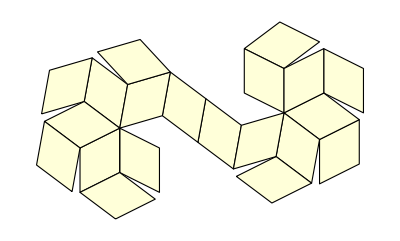

```mathematica
PolyhedronData["RhombicIcosahedron","Net"]
```

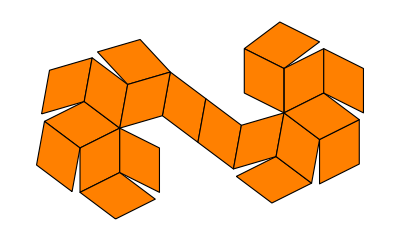

```mathematica
PolyhedronData["RhombicIcosahedron","Net","Colored"]
```

## Properties

```mathematica
<<MathWorld`PolyhedronOperations`
```

```mathematica
p=PolyhedronData[pname="RhombicIcosahedron","Polyhedron"]
```

Polyhedron[…]

### Centroid

```mathematica
Graphics3D[{AbsolutePointSize[10],
Point[{0,0,0}],{Blue,Point[PolyhedronData[pname,"Centroid"]]},Opacity[.2],PolyhedronData[pname,"GraphicsComplex"]}]
```

-Graphics3D-

```mathematica
PolyhedronData[pname,"Centroid"]
```

{0,0,0}

```mathematica
RegionCentroid[p]//FullSimplify//Timing
```

{0.619079,{0,0,0}}

```mathematica
PolyhedronCentroid[p]//FullSimplify//Timing
```

{13.2052,{0,0,0}}

### Circumsphere

```mathematica
PolyhedronData[pname,"Circumsphere"]
```

Missing[NotApplicable]

```mathematica
Circumsphere[p]
```

Circumsphere::indep: Circumsphere does not exist for Polyhedron[{{-1-1/(√5),0,1/(2 √5)},{1/10 (-5-3 √5),Root[1-5 Power[«2»]+5 Power[«2»]&,1,0],-1/(2 √5)},{1/10 (-5-3 √5),√(1/10 (5+√5)),-1/(2 √5)},{-2/(√5),0,-3/(2 √5)},{1/10 (-5-√5),Root[1-5 Power[«2»]+5 Power[«2»]&,2,0],3/(2 √5)},{«1»},{-1/(√5),-√(1+2 «1»),1/(2 «1»)},{-1/(√5),√(1+2/(√5)),1/(2 √5)},{1/10 (-5+√5),Root[1-5 Power[«2»]+5 Power[«2»]&,1,0],-3/(2 √5)},{1/10 (-5+√5),√(1/10 (5+√5)),-3/(2 √5)},«12»},«1»].

Circumsphere[Polyhedron[…]]

```mathematica
(sphere=MyCircumsphere[p])//Timing
```

{0.070992,{}}

### Convex

```mathematica
ConvexPolyhedronQ[p]
```

True

### DihedralAngles

```mathematica
PolyhedronData[pname,"DihedralAngles"]//Tally
```

{{(4 π)/5,30},{(3 π)/5,10}}

```mathematica
DihedralAngles[p]//FullSimplify//Tally//Timing
```

{{(4 π)/5,30},{(3 π)/5,10}}

### EdgeLengths

```mathematica
PolyhedronData[pname,"EdgeLengths"]
```

{1}

```mathematica
PolyhedronData[pname,"Lines"]/.Line[l_]:>EuclideanDistance@@l//FullSimplify//Union//Quiet
```

{1}

### Faces

```mathematica
FullSimplify[Norm/@Subtract@@@Transpose[Partition[Polyhedron[RhombicIcosahedron][[1,1]],2]]]
```

{1/4 (5+√5),(√5)/2}

```mathematica
FullSimplify[Divide@@%]
```

1/2 (1+√5)

```mathematica
FunctionExpand[GoldenRatio]
```

1/2 (1+√5)

```mathematica
rhomb=RhombicTriacontahedronExact[[1]];
```

```mathematica
RootReduce//@rhomb
```

Polygon[{{Root[5-80 #1^2+256 #1^4&,4],1/8 (-5-3 √5),Root[5-80 #1^2+256 #1^4&,3]},{Root[5-80 #1^2+256 #1^4&,4],1/8 (-5-3 √5),Root[5-160 #1^2+256 #1^4&,1]},{Root[5-80 #1^2+256 #1^4&,1],1/8 (-5-3 √5),Root[5-80 #1^2+256 #1^4&,2]},{Root[5-80 #1^2+256 #1^4&,1],1/8 (-5-3 √5),Root[5-160 #1^2+256 #1^4&,4]}}]

```mathematica
v=FullSimplify[ToRadicals/@%8][[1]]
```

{{1/4 √(1/2 (5+√5)),1/8 (-5-3 √5),√(5/32-(√5)/32)},{1/4 √(1/2 (5+√5)),1/8 (-5-3 √5),-1/4 √(5+2 √5)},{-1/4 √(1/2 (5+√5)),1/8 (-5-3 √5),-1/4 √(1/2 (5-√5))},{-1/4 √(1/2 (5+√5)),1/8 (-5-3 √5),1/4 √(5+2 √5)}}

```mathematica
s=FullSimplify[Sqrt[#.#]&[v[[1]]-v[[2]]]]
```

1/4 √(5/2 (5+√5))

```mathematica
b=FullSimplify[Sqrt[#.#]&[v[[1]]-v[[3]]]]
```

(√5)/2

```mathematica
a=FullSimplify[Sqrt[#.#]&[v[[2]]-v[[4]]]]
```

1/4 (5+√5)

```mathematica
planerhomb={{a,0},{0,b},{-a,0},{0,-b}};
Show[Graphics[{{GrayLevel[.8],Polygon[planerhomb]},Line[Append[planerhomb,planerhomb[[1]]]]}],AspectRatio->Automatic]
```

⁃Graphics⁃

### GeneralizedDiameter

```mathematica
PolyhedronData[pname,"GeneralizedDiameter"]
```

√(5+8/(√5))

```mathematica
GeneralizedDiameter[p]//FullSimplify//Quiet
```

√(5+8/(√5))

### InertiaTensor

```mathematica
PolyhedronData[pname,"InertiaTensor"]
```

{{1/100 (45+2 √5),0,0},{0,1/100 (45+2 √5),0},{0,0,2/5+3/(5 √5)}}

```mathematica
MomentOfInertia[p,{0,0,0}]/Volume[p]//RootReduce//Timing
```

$Aborted

```mathematica
PolyhedronInertiaTensor[p]//Timing
```

### Insphere

```mathematica
PolyhedronData[pname,"Insphere"]
```

Missing[NotApplicable]

```mathematica
Insphere[p]
```

Insphere::indep: Insphere does not exist for Polyhedron[{{-1-1/(√5),0,1/(2 √5)},{1/10 (-5-3 √5),Root[1-5 Power[«2»]+5 Power[«2»]&,1,0],-1/(2 √5)},{1/10 (-5-3 √5),√(1/10 (5+√5)),-1/(2 √5)},{-2/(√5),0,-3/(2 √5)},{1/10 (-5-√5),Root[1-5 Power[«2»]+5 Power[«2»]&,2,0],3/(2 √5)},{«1»},{-1/(√5),-√(1+2 «1»),1/(2 «1»)},{-1/(√5),√(1+2/(√5)),1/(2 √5)},{1/10 (-5+√5),Root[1-5 Power[«2»]+5 Power[«2»]&,1,0],-3/(2 √5)},{1/10 (-5+√5),√(1/10 (5+√5)),-3/(2 √5)},«12»},«1»].

Insphere[Polyhedron[…]]

```mathematica
sphere=MyInsphere[p]
```

$Aborted

### MeanCylindricalRadius

```mathematica
NIntegrate[√(x^2+y^2),{x,y,z}∈p]/PolyhedronData[pname,"Volume"]//Timing
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{14.0307,0.754852}

```mathematica
(i=Integrate[√(x^2+y^2),{x,y,z}∈p]/PolyhedronData[pname,"Volume"])//Timing
```

```mathematica
N[i]
```

### MeanSquareCylindricalRadius

```mathematica
NIntegrate[x^2+y^2,{x,y,z}∈p]/PolyhedronData[pname,"Volume"]//Timing
```

{0.329494,0.668328}

```mathematica
(i=Integrate[x^2+y^2,{x,y,z}∈p]/PolyhedronData[pname,"Volume"]//FullSimplify)//Timing
```

{2.4587,2/5+3/(5 √5)}

```mathematica
N[i]
```

0.668328

### MeanSphericalRadius

```mathematica
NIntegrate[√(x^2+y^2+z^2),{x,y,z}∈p]/PolyhedronData[pname,"Volume"]//Timing
```

{8.06578,0.875737}

```mathematica
(i=Integrate[√(x^2+y^2+z^2),{x,y,z}∈p]/PolyhedronData[pname,"Volume"])//Timing
```

```mathematica
N[i]
```

### MeanSquareSphericalRadius

```mathematica
NIntegrate[x^2+y^2+z^2,{x,y,z}∈p]/PolyhedronData[pname,"Volume"]//Timing
```

{0.34306,0.828885}

```mathematica
(i=Integrate[x^2+y^2+z^2,{x,y,z}∈p]/PolyhedronData[pname,"Volume"]//FullSimplify)//Timing
```

{2.1638,1/100 (65+8 √5)}

```mathematica
N[i]
```

0.828885

### Midsphere

```mathematica
sphere=PolyhedronData[pname,"Midsphere"]
```

Missing[NotApplicable]

```mathematica
(sphere=Midsphere[p])//Timing
```

$Aborted

### SurfaceArea

```mathematica
PolyhedronData[pname,"SurfaceArea"]
```

8 √5

```mathematica
SurfaceArea[p]//RootReduce//Timing
```

$Aborted

```mathematica
Total[Area/@PolyhedronData[pname,"Polygons"]]//RootReduce//Timing
```

### VertexSubsetHulls

```mathematica
PolyhedronData[pname,"VertexSubsetHulls"]
```

{RhombicIcosahedron→{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22}}}

#### Platonic

```mathematica
(h=VertexSubsetHulls[p,"Platonic","Skip"->{}])//Timing
```

Finding equilateral triangles...

Finding potential tetrahedra from equilateral triangles...

Finding tetrahedra from potential candidates...

Finding cubes from tetrahedra...

Finding dodecahedron from cubes...

Finding octahedra by building up from equilateral triangles...

Finding dodecahedra from octahedra...

Finding icosahedra by building up from equilateral triangles...

{0.056358,{}}

### Volume

```mathematica
PolyhedronData[pname,"Volume"]
```

2 √(5+2 √5)

```mathematica
Volume[p]//FullSimplify
```

2 √(5+2 √5)

```mathematica
PolyhedronVolume[p,Method->"GaussLaw"]//FullSimplify
```

2 √(5+2 √5)

## Perspective projections

```mathematica
Manipulate[PolyhedronProjectionGraph[PolyhedronData["Cuboctahedron","Polyhedron"],{a,b,c}],{a,-1,1},{b,-1,1},{c,-1,1}]
```

### XXX

```mathematica
PolyhedronProjectionGraph[PolyhedronData["DuererSolid","Polyhedron"],]
```

## Construction as a zonohedron

Diagonals of the 5-antiprism

```mathematica
e=KSubsets[PolyhedronVertices[Polyhedron[Antiprism[5]]],2];
n=RootReduce/@Norm/@(Subtract@@@e);
```

```mathematica
Length[diags=Select[e,RootReduce@Norm[Subtract@@#]==Max[n]&]]
```

5

```mathematica
Show[Graphics3D[{
Line/@diags,
Red,PointSize[.05],Point[{0,0,0}]
}
],Boxed->False]
```

⁃Graphics3D⁃

```mathematica
v=ToRadicals[FullSimplify[-Subtract@@@diags]]
```

{{√(2+2/(√5)),0,√(1/10 (5+√5))},{√(1/10 (5-√5)),1/2 (1+√5),√(1/10 (5+√5))},{√(1/10 (5-√5)),1/2 (-1-√5),√(1/10 (5+√5))},{√(1+2/(√5)),1,-√(1/2+1/(2 √5))},{√(1+2/(√5)),-1,-√(1/2+1/(2 √5))}}

```mathematica
Show[Graphics3D[Zonohedron[v]],Boxed->False]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/2\ (-1 - √5) + 1/2\ (1 + √5). More…

General::stop: Further output of N :: "meprec" will be suppressed during this calculation. More…

⁃Graphics3D⁃

## Exact construction

```mathematica
<<MiscPolyhedra`
```

```mathematica
(*rotate 1/10 of a turn and flip z*)invertedPoly[l_List]:=Polygon[Append[{{Cos[Pi/5],Sin[Pi/5]},{-Sin[Pi/5],Cos[Pi/5]}}.Take[#,2],-Last[#]]&/@l]
```

```mathematica
(*shift down 1/2 edge length*)shiftedPoly[l_List]:=Polygon[Append[Take[#,2],Last[#]-Sqrt[5/2(5+Sqrt[5])]/8]&/@l]

RhombicIcosahedronExact:=Module[{ri=Polyhedron[RhombicTriacontahedron],cap},cap=ri[[{7,8,9,10,4,17,19,20,25,26}]]/.Polygon:>shiftedPoly;
{cap,cap/.Polygon:>invertedPoly}]
```

```mathematica
Show[Graphics3D[poly=Orient[RhombicIcosahedronExact]],Boxed->False]
```

⁃Graphics3D⁃

```mathematica
<<Simplify`
Off[N::"meprec"];
```

```mathematica
poly2=Map[ToExact,Flatten[poly],{3}];
(v=PolyhedronVertices[poly2])//InputForm
First/@poly2/.Thread[v->Range[Length[v]]]
```

{{19,5,7,9},{20,10,8,6},{7,11,21,23},{8,24,21,12},{20,16,19,22},{2,12,21,11},{5,2,11,7},{6,8,12,2},{19,16,2,5},{20,6,2,16},{7,17,3,9},{14,10,20,22},{21,18,15,17},{4,18,8,10},{19,9,13,22},{15,18,4,1},{17,15,1,3},{1,4,10,14},{3,1,13,9},{13,1,14,22}}

{{0, 0, -Sqrt[125/128 + (25*Sqrt[5])/128]}, {0, 0, Sqrt[125/128 + (25*Sqrt[5])/128]}, 
 {-Sqrt[(5 - Sqrt[5])/2]/4, (-5 - Sqrt[5])/8, -Sqrt[45/128 + (9*Sqrt[5])/128]}, 
 {-Sqrt[(5 - Sqrt[5])/2]/4, (5 + Sqrt[5])/8, -Sqrt[45/128 + (9*Sqrt[5])/128]}, 
 {Sqrt[(5 - Sqrt[5])/2]/4, (-5 - Sqrt[5])/8, Sqrt[45/128 + (9*Sqrt[5])/128]}, 
 {Sqrt[(5 - Sqrt[5])/2]/4, (5 + Sqrt[5])/8, Sqrt[45/128 + (9*Sqrt[5])/128]}, 
 {-Sqrt[5/32 + Sqrt[5]/32], (-5 - 3*Sqrt[5])/8, Sqrt[5/128 + Sqrt[5]/128]}, 
 {-Sqrt[5/32 + Sqrt[5]/32], (5 + 3*Sqrt[5])/8, Sqrt[5/128 + Sqrt[5]/128]}, 
 {Sqrt[5/32 + Sqrt[5]/32], (-5 - 3*Sqrt[5])/8, -Sqrt[5/128 + Sqrt[5]/128]}, 
 {Sqrt[5/32 + Sqrt[5]/32], (5 + 3*Sqrt[5])/8, -Sqrt[5/128 + Sqrt[5]/128]}, 
 {-Sqrt[5/16 + Sqrt[5]/8], -Sqrt[5]/4, Sqrt[45/128 + (9*Sqrt[5])/128]}, 
 {-Sqrt[5/16 + Sqrt[5]/8], Sqrt[5]/4, Sqrt[45/128 + (9*Sqrt[5])/128]}, 
 {Sqrt[5/16 + Sqrt[5]/8], -Sqrt[5]/4, -Sqrt[45/128 + (9*Sqrt[5])/128]}, 
 {Sqrt[5/16 + Sqrt[5]/8], Sqrt[5]/4, -Sqrt[45/128 + (9*Sqrt[5])/128]}, 
 {-Sqrt[5/8 + Sqrt[5]/8], 0, -Sqrt[45/128 + (9*Sqrt[5])/128]}, 
 {Sqrt[5/8 + Sqrt[5]/8], 0, Sqrt[45/128 + (9*Sqrt[5])/128]}, 
 {-Sqrt[25/32 + (11*Sqrt[5])/32], (-5 - Sqrt[5])/8, -Sqrt[5/128 + Sqrt[5]/128]}, 
 {-Sqrt[25/32 + (11*Sqrt[5])/32], (5 + Sqrt[5])/8, -Sqrt[5/128 + Sqrt[5]/128]}, 
 {Sqrt[25/32 + (11*Sqrt[5])/32], (-5 - Sqrt[5])/8, Sqrt[5/128 + Sqrt[5]/128]}, 
 {Sqrt[25/32 + (11*Sqrt[5])/32], (5 + Sqrt[5])/8, Sqrt[5/128 + Sqrt[5]/128]}, 
 {-Sqrt[5/4 + Sqrt[5]/2], 0, Sqrt[5/128 + Sqrt[5]/128]}, 
 {Sqrt[5/4 + Sqrt[5]/2], 0, -Sqrt[5/128 + Sqrt[5]/128]}, 
 {Root[5 - 400*#1^2 + 256*#1^4 & , 1, 0], (-5 - Sqrt[5])/8, -Sqrt[5/128 + Sqrt[5]/128]}, 
 {Root[5 - 400*#1^2 + 256*#1^4 & , 1, 0], (5 + Sqrt[5])/8, -Sqrt[5/128 + Sqrt[5]/128]}}

## Net Construction

### Weisstein (Feb 2019) exact version from Izador Hafner Demonstration

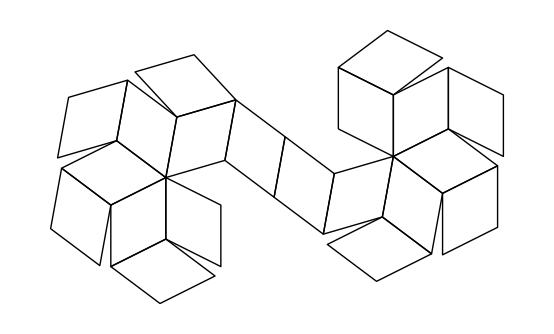
```mathematica
v=Union[Flatten[-Graphics-[[1,All,1]],1]];
```

```mathematica
Length[v]
```

42

```mathematica
sub=Subsets[Range[42],{2}];
```

```mathematica
i=Select[sub,EuclideanDistance@@v[[#]]==1&]
```

{{1,3},{1,5},{2,4},{2,8},{3,6},{3,8},{4,9},{5,6},{6,7},{6,12},{7,11},{7,13},{8,9},{8,12},{9,14},{10,14},{10,15},{11,16},{12,13},{12,14},{12,17},{12,19},{13,16},{13,18},{14,20},{15,20},{17,18},{19,20},{19,21},{20,22},{21,22},{21,23},{22,25},{23,25},{23,29},{24,28},{24,29},{25,31},{26,27},{26,31},{27,30},{27,32},{28,33},{29,31},{29,33},{30,35},{31,32},{31,34},{31,37},{32,35},{32,38},{33,34},{34,36},{34,39},{36,40},{37,38},{37,39},{37,41},{38,42},{39,40},{41,42}}

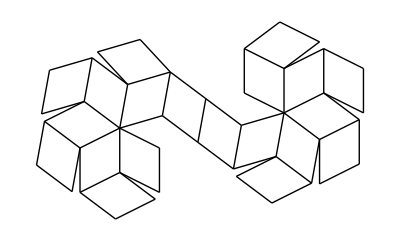

```mathematica
GraphicsComplex[v,Line[i]]//Graphics
```

```mathematica
exact=RootApproximant[v,2,Method->{"DegreeCost"->2}]
```

```mathematica
exact={{1/25 (-108-4 √5),1/25 (31-32 √5)},{1/25 (-132+8 √5),1/25 (24-16 √5)},{1/25 (-108-2 √5),1/25 (31-21 √5)},{1/25 (-132+10 √5),1/25 (24-5 √5)},{1/25 (-88-4 √5),1/25 (16-32 √5)},{1/25 (-88-2 √5),1/25 (16-21 √5)},{1/25 (-88-2 √5),1/25 (-9-21 √5)},{1/25 (-108+8 √5),1/25 (31-16 √5)},{1/25 (-108+10 √5),1/25 (31-5 √5)},{1/125 (-440+12 √5),1/125 (80+16 √5)},{1/25 (-68-2 √5),1/25 (-24-21 √5)},{1/25 (-88+8 √5),1/25 (16-16 √5)},{1/25 (-88+8 √5),1/25 (-9-16 √5)},{1/25 (-88+10 √5),1/25 (16-5 √5)},{1/125 (-320+12 √5),1/125 (115+16 √5)},{1/25 (-68+8 √5),1/25 (-24-16 √5)},{1/25 (-88+18 √5),1/25 (16-21 √5)},{1/25 (-88+18 √5),1/25 (-9-21 √5)},{1/25 (-64+8 √5),1/25 (23-16 √5)},{1/25 (-64+10 √5),1/25 (23-5 √5)},{1/25 (-44+8 √5),1/25 (8-16 √5)},{1/25 (-44+10 √5),1/25 (8-5 √5)},{1/25 (-24+8 √5),1/25 (-7-16 √5)},{-2/(5 √5),-21/(5 √5)},{1/25 (-24+10 √5),1/25 (-7-5 √5)},{0,0},{0,1},{1/25 (20-2 √5),1/25 (-15-21 √5)},{8/(5 √5),-16/(5 √5)},{4/5,8/5},{2/(√5),-1/(√5)},{2/(√5),1/5 (5-√5)},{1/25 (20+8 √5),1/25 (-15-16 √5)},{1/5 (4+2 √5),1/5 (-3-√5)},{1/5 (4+2 √5),1/5 (8-√5)},{1/5 (4+2 √5),1/5 (-8-√5)},{4/(√5),0},{4/(√5),1},{1/5 (4+4 √5),-3/5},{1/5 (4+4 √5),-8/5},{6/(√5),-1/(√5)},{6/(√5),1/5 (5-√5)}};
```

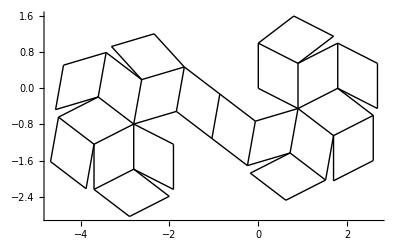

```mathematica
Graphics[GraphicsComplex[exact,Line[i]],Axes->True]
```

```mathematica
FullSimplify[EuclideanDistance@@@(exact[[#]]&/@i)]//Union
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/25 (-88-2 √5)+1/25 (88+2 √5).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/25 (88-8 √5)+1/25 (-88+8 √5).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/25 (88-18 √5)+1/25 (-88+18 √5).

General::stop: Further output of N::meprec will be suppressed during this calculation.

{1}

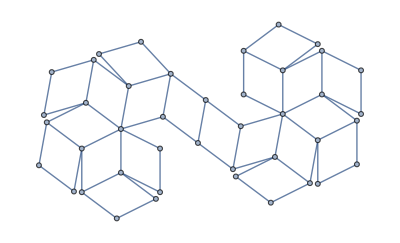

```mathematica
g=System`Graph[Range[42],UndirectedEdge@@@i,VertexCoordinates->exact]
```

```mathematica
faces=System`FindCycle[g,{4},All][[All,All,1]]
```

{{37,41,42,38},{27,32,35,30},{21,23,25,22},{34,36,40,39},{37,31,34,39},{8,12,14,9},{6,7,13,12},{33,29,31,34},{4,9,8,2},{12,13,18,17},{32,38,37,31},{32,27,26,31},{3,6,12,8},{24,28,33,29},{20,22,21,19},{20,14,12,19},{23,25,31,29},{11,16,13,7},{10,15,20,14},{1,3,6,5}}

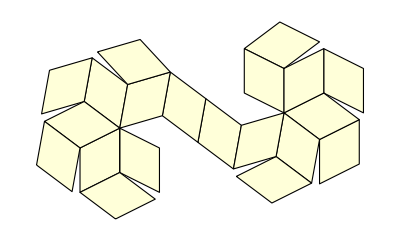

```mathematica
Graphics[{FaceForm[LightYellow],EdgeForm[Black],GraphicsComplex[exact,Polygon[faces]]}]
```

```mathematica
Oriented2DQ[p_]:=Chop[N[Total[Det/@Partition[p,2,1,1]],20]]>0
```

```mathematica
orientations=Oriented2DQ/@(v[[#]]&/@faces)
```

{True,True,True,True,True,True,True,False,False,True,False,True,True,True,False,True,False,True,False,False}

```mathematica
newfaces=If[#,#2,Reverse[#2]]&@@@Transpose[{orientations,faces}]
```

{{37,41,42,38},{27,32,35,30},{21,23,25,22},{34,36,40,39},{37,31,34,39},{8,12,14,9},{6,7,13,12},{34,31,29,33},{2,8,9,4},{12,13,18,17},{31,37,38,32},{32,27,26,31},{3,6,12,8},{24,28,33,29},{19,21,22,20},{20,14,12,19},{29,31,25,23},{11,16,13,7},{14,20,15,10},{5,6,3,1}}

```mathematica
Oriented2DQ/@(v[[#]]&/@newfaces)
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Graphics[{FaceForm[LightYellow],EdgeForm[Black],GraphicsComplex[exact,Polygon[newfaces]]}]
```

-Graphics-

```mathematica
EuclideanDistance@@@Flatten[Partition[#,2,1,1]&/@Flatten[Normal[GraphicsComplex[exact,Polygon[newfaces]]]][[All,1]],1]//FullSimplify//Union
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/5 (-4-2 √5)+1/5 (4+2 √5).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/5 (-4-4 √5)+1/5 (4+4 √5).

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/25 (-88-2 √5)+1/25 (88+2 √5).

General::stop: Further output of N::meprec will be suppressed during this calculation.

{1}

```mathematica
Flatten[PolygonAngle/@Normal[GraphicsComplex[exact,Polygon[newfaces]]][[1]]]//FullSimplify//Union
```

{ArcCos[-1/(√5)],ArcSec[√5]}

### Izador Hafner Demonstration

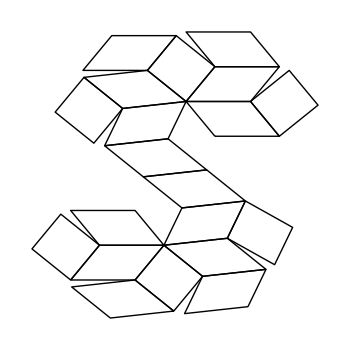
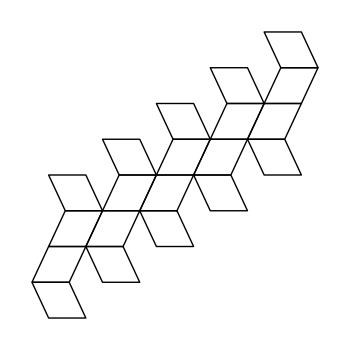
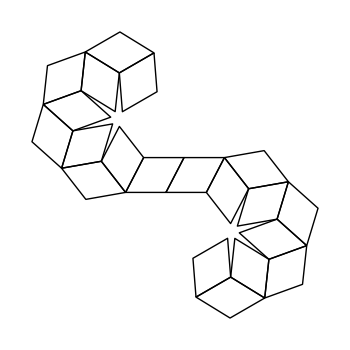
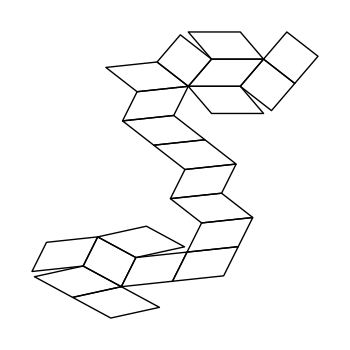
```mathematica
GraphicsRow[{-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

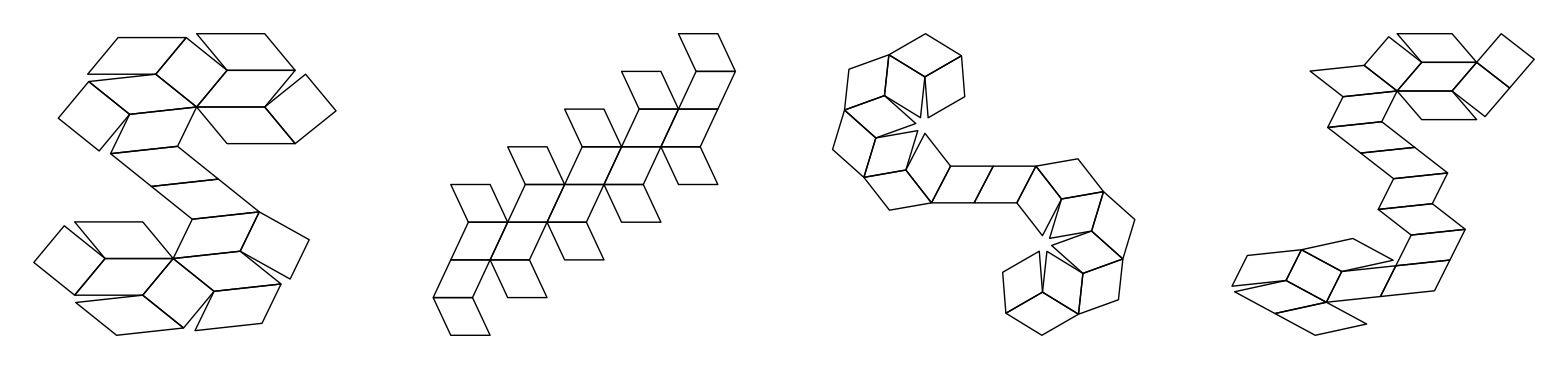

## Vertex subset hulls

```mathematica
p="RhombicIcosahedron";
```

### Platonic

```mathematica
(h=VertexSubsetHulls[p,"Platonic","Skip"->{}])//Timing
```

Finding equilateral triangles...

Finding potential tetrahedra from equilateral triangles...

Finding tetrahedra from potential candidates...

Finding cubes from tetrahedra...

Finding dodecahedron from cubes...

Finding octahedra by building up from equilateral triangles...

Finding dodecahedra from octahedra...

Finding icosahdra by building up from equilateral triangles...

{0.111174,{}}

## PolyhedronData

```mathematica
Graphics3D[{FaceForm[Blue,Red],Orient@FullSimplify[Polyhedron[RhombicIcosahedron]]}]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating {{1/4 √1/2 (5 + Times[« 2 »]) - √25/32 + 11/32 Power[« 2 »], 1/8 (-5 - √5) + 1/8 (5 + √5), -√5/128 + 1/128 Power[« 2 »] + √45/128 + 9 √5/128}, « 1 »}.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating {{√5/32 + √5/32 - √25/32 + 11/32 Power[« 2 »], 1/8 (-5 - √5) + 1/8 (5 + 3 √5), -2 √5/128 + √5/128}, {1/4 √1/2 (5 + Times[« 2 »]) - √25/32 + 11/32 Power[« 2 »], « 1 », -√5/« 3 » + « 1 » + √« 1 »}}.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating {515,{1,1,-√(5+1/3 1)+1}}.

General::stop: Further output of N will be suppressed during this calculation.

-Graphics3D-

```mathematica
PolyhedronDataString[Orient@FullSimplify[Polyhedron[RhombicIcosahedron]],
"StandardName"->"RhombicIcosahedron",
"Information"->"RhombicIcosahedron",
"Name"->"rhombic icosahedron",
"Classes"->{"Convex","Zonohedron"},
Debug->True,
TimeConstraint->600
]
```